# Mathematica for Bioinformatics

## Chapter 7: Proteomic Data

## Amino Acids

```mathematica
aminoAcids=EntityClass["Chemical", "AminoAcids"];
```

```mathematica
ChemicalData["AminoAcids","Properties"]//Short
```

{AcidityConstants,AdjacencyMatrix,«95»,VertexTypes,Viscosity}

```mathematica
ChemicalData["AminoAcids","Properties"][[1;;20]]
```

{AcidityConstants,AdjacencyMatrix,AlternateNames,AtomPositions,AutoignitionPoint,BeilsteinNumber,BlackStructureDiagram,BoilingPoint,BondTally,BoundaryMeshRegion,CASNumber,CHBlackStructureDiagram,CHColorStructureDiagram,CIDNumber,Codons,ColorStructureDiagram,CombustionHeat,CompoundFormulaDisplay,CompoundFormulaString,CriticalPressure}

```mathematica
ChemicalData["AminoAcids","Name"]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
aminoAcid2Codon=AssociationThread[ChemicalData["AminoAcids","Name"]-> ChemicalData["AminoAcids","Codons"]]
```

<|glycine→{GGU,GGC,GGA,GGG},L-alanine→{GCU,GCC,GCA,GCG},L-serine→{UCU,UCC,UCA,UCG,AGU,AGC},L-proline→{CCU,CCC,CCA,CCG},L-valine→{GUU,GUC,GUA,GUG},L-threonine→{ACU,ACC,ACA,ACG},L-cysteine→{UGU,UGC},L-isoleucine→{AUU,AUC,AUA},L-leucine→{UUA,UUG,CUU,CUC,CUA,CUG},L-asparagine→{AAU,AAC},L-aspartic acid→{GAU,GAC},L-glutamine→{CAA,CAG},L-lysine→{AAA,AAG},L-glutamic acid→{GAA,GAG},L-methionine→{AUG},L-histidine→{CAU,CAC},L-phenylalanine→{UUU,UUC},L-arginine→{CGU,CGC,CGA,CGG,AGA,AGG},L-tyrosine→{UAU,UAC},L-tryptophan→{UGG}|>

```mathematica
codon2AminoAcid=Join[Join@@(AssociationThread[#[[2]],ConstantArray[#[[1]],Length[#[[2]]]]]&/@Transpose[{ChemicalData["AminoAcids","Name"], ChemicalData["AminoAcids","Codons"]}]) , <|"UAA"-> "Stop Codon","UAG"-> "Stop Codon","UGA"-> "Stop Codon"|>]
```

<|GGU→glycine,GGC→glycine,GGA→glycine,GGG→glycine,GCU→L-alanine,GCC→L-alanine,GCA→L-alanine,GCG→L-alanine,UCU→L-serine,UCC→L-serine,UCA→L-serine,UCG→L-serine,AGU→L-serine,AGC→L-serine,CCU→L-proline,CCC→L-proline,CCA→L-proline,CCG→L-proline,GUU→L-valine,GUC→L-valine,GUA→L-valine,GUG→L-valine,ACU→L-threonine,ACC→L-threonine,ACA→L-threonine,ACG→L-threonine,UGU→L-cysteine,UGC→L-cysteine,AUU→L-isoleucine,AUC→L-isoleucine,AUA→L-isoleucine,UUA→L-leucine,UUG→L-leucine,CUU→L-leucine,CUC→L-leucine,CUA→L-leucine,CUG→L-leucine,AAU→L-asparagine,AAC→L-asparagine,GAU→L-aspartic acid,GAC→L-aspartic acid,CAA→L-glutamine,CAG→L-glutamine,AAA→L-lysine,AAG→L-lysine,GAA→L-glutamic acid,GAG→L-glutamic acid,AUG→L-methionine,CAU→L-histidine,CAC→L-histidine,UUU→L-phenylalanine,UUC→L-phenylalanine,CGU→L-arginine,CGC→L-arginine,CGA→L-arginine,CGG→L-arginine,AGA→L-arginine,AGG→L-arginine,UAU→L-tyrosine,UAC→L-tyrosine,UGG→L-tryptophan,UAA→Stop Codon,UAG→Stop Codon,UGA→Stop Codon|>

```mathematica
Length[%]
```

64

```mathematica
aminoAcidAbbreviations=<|"1letter"->AssociationThread[#[[All,1]]-> #[[All,2]]] ,"3letter"-> AssociationThread[#[[All,1]]-> #[[All,3]]]|>&@{{"glycine","G","Gly"},{"L-alanine","A","Ala"},{"L-serine","S","Ser"},{"L-proline","P","Pro"},{"L-valine","V","Val"},{"L-threonine","T","Thr"},{"L-cysteine","C","Cys"},{"L-leucine","L","Leu"},{"L-asparagine","N","Asn"},{"L-aspartic acid","D","Asp"},{"L-glutamine","Q","Gln"},{"L-lysine","K","Lys"},{"L-glutamic acid","E","Glu"},{"L-methionine","M","Met"},{"L-histidine","H","His"},{"L-phenylalanine","F","Phe"},{"L-arginine","R","Arg"},{"L-tyrosine","Y","Tyr"},{"L-tryptophan","W","Trp"},{"L-isoleucine","I","Ile"},{"Stop Codon","*","*"}};
```

```mathematica
codon2AA=Query[All,aminoAcidAbbreviations["1letter"][#]&]@codon2AminoAcid
```

<|GGU→G,GGC→G,GGA→G,GGG→G,GCU→A,GCC→A,GCA→A,GCG→A,UCU→S,UCC→S,UCA→S,UCG→S,AGU→S,AGC→S,CCU→P,CCC→P,CCA→P,CCG→P,GUU→V,GUC→V,GUA→V,GUG→V,ACU→T,ACC→T,ACA→T,ACG→T,UGU→C,UGC→C,AUU→I,AUC→I,AUA→I,UUA→L,UUG→L,CUU→L,CUC→L,CUA→L,CUG→L,AAU→N,AAC→N,GAU→D,GAC→D,CAA→Q,CAG→Q,AAA→K,AAG→K,GAA→E,GAG→E,AUG→M,CAU→H,CAC→H,UUU→F,UUC→F,CGU→R,CGC→R,CGA→R,CGG→R,AGA→R,AGG→R,UAU→Y,UAC→Y,UGG→W,UAA→*,UAG→*,UGA→*|>

```mathematica
CanonicalName[#]&/@EntityValue["Chemical","Properties"][[1;;10]]
```

{AcidityConstants,AdjacencyMatrix,AlternateNames,AtomPositions,AutoignitionPoint,BeilsteinNumber,BlackStructureDiagram,BoilingPoint,BondCounts,BondEnergies}

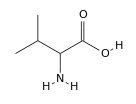
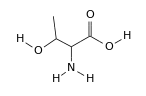
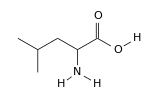
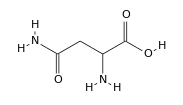
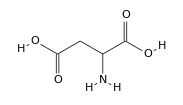
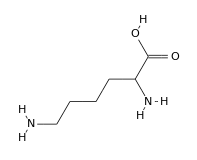
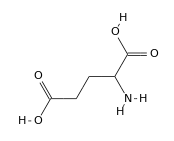
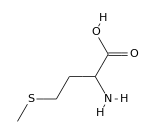
<|glycine→-Graphics-,L-alanine→-Graphics-,L-serine→-Graphics-,L-proline→-Graphics-,L-valine→-Graphics-,L-threonine→-Graphics-,L-cysteine→-Graphics-,L-leucine→-Graphics-,L-asparagine→-Graphics-,L-aspartic acid→-Graphics-,L-glutamine→-Graphics-,L-lysine→-Graphics-,L-glutamic acid→-Graphics-,L-methionine→-Graphics-,DL-histidine→-Graphics-,L-phenylalanine→-Graphics-,L-arginine→-Graphics-,L-tyrosine→-Graphics-,L-tryptophan→-Graphics-,L-isoleucine→-Graphics-|>

```mathematica
EntityValue[#,"BlackStructureDiagram","EntityAssociation"]& @aminoAcids
```

```mathematica
EntityList[EntityClass["Chemical","AminoAcids"]]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,DL-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,L-isoleucine}

amino acids

WolframAlphaQueryResults

AACATTTGGCAGCTGAAAAAGGATGTGGATA

WolframAlphaQueryResults

```mathematica
WolframAlpha["AATCATTTGGCAGCTGAAAAAGGATGTGGATA",{{"AminoAcidSequence",1},"FormattedData"},PodStates->{"AminoAcidSequence__All reading frames"}]
```

5'-3'  frame 1 | AAU | CAU | UUG | GCA | GCU | GAA | AAA | GGA
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
N | H | L | A | A | E | K | G
UGU | GGA
↓ | ↓
C | G
5'-3'  frame 2 | AUC | AUU | UGG | CAG | CUG | AAA | AAG | GAU
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
I | I | W | Q | L | K | K | D
GUG | GAU
↓ | ↓
V | D
5'-3'  frame 3 | UCA | UUU | GGC | AGC | UGA | AAA | AGG | AUG
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
S | F | G | S | - | K | R | M
UGG | AUA
↓ | ↓
W | I
3'-5'  frame 1 | UAU | CCA | CAU | CCU | UUU | UCA | GCU | GCC
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
Y | P | H | P | F | S | A | A
AAA | UGA
↓ | ↓
K | -
3'-5'  frame 2 | AUC | CAC | AUC | CUU | UUU | CAG | CUG | CCA
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
I | H | I | L | F | Q | L | P
AAU | GAU
↓ | ↓
N | D
3'-5'  frame 3 | UCC | ACA | UCC | UUU | UUC | AGC | UGC | CAA
↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
S | T | S | F | F | S | C | Q
AUG | AUU
↓ | ↓
M | I

```mathematica
WolframAlpha["AATCATTTGGCAGCTGAAAAAGGATGTGGATA",{{"AminoAcidSequence",1},"ComputableData"},PodStates->{"AminoAcidSequence__All reading frames"}]
```

{{5'-3'  frame 1,{{{AAU,CAU,UUG,GCA,GCU,GAA,AAA,GGA},{↓,↓,↓,↓,↓,↓,↓,↓},{N,H,L,A,A,E,K,G}},{{UGU,GGA},{↓,↓},{C,G}}}},{5'-3'  frame 2,{{{AUC,AUU,UGG,CAG,CUG,AAA,AAG,GAU},{↓,↓,↓,↓,↓,↓,↓,↓},{I,I,W,Q,L,K,K,D}},{{GUG,GAU},{↓,↓},{V,D}}}},{5'-3'  frame 3,{{{UCA,UUU,GGC,AGC,UGA,AAA,AGG,AUG},{↓,↓,↓,↓,↓,↓,↓,↓},{S,F,G,S,-,K,R,M}},{{UGG,AUA},{↓,↓},{W,I}}}},{3'-5'  frame 1,{{{UAU,CCA,CAU,CCU,UUU,UCA,GCU,GCC},{↓,↓,↓,↓,↓,↓,↓,↓},{Y,P,H,P,F,S,A,A}},{{AAA,UGA},{↓,↓},{K,-}}}},{3'-5'  frame 2,{{{AUC,CAC,AUC,CUU,UUU,CAG,CUG,CCA},{↓,↓,↓,↓,↓,↓,↓,↓},{I,H,I,L,F,Q,L,P}},{{AAU,GAU},{↓,↓},{N,D}}}},{3'-5'  frame 3,{{{UCC,ACA,UCC,UUU,UUC,AGC,UGC,CAA},{↓,↓,↓,↓,↓,↓,↓,↓},{S,T,S,F,F,S,C,Q}},{{AUG,AUU},{↓,↓},{M,I}}}}}

```mathematica
codon2AA/@StringReplace[(StringPartition["AATCATTTGGCAGCTGAAAAAGGATGTGGATA",3]),"T"->"U"]
```

{N,H,L,A,A,E,K,G,C,G}

## Protein Information

```mathematica
ProteinData["JUN","Properties"]
```

{AdditionalAtomPositions,AdditionalAtomTypes,AtomPositions,AtomRoles,AtomTypes,BiologicalProcesses,CellularComponents,ChainLabels,ChainSequences,DihedralAngles,DNACodingSequence,DNACodingSequenceLength,DomainIDs,DomainPositions,Domains,Gene,GeneID,GyrationRadius,Memberships,MolecularFunctions,MolecularWeight,MoleculePlot,Name,NCBIAccessions,PDBIDList,PrimaryPDBID,SecondaryStructureRules,Sequence,SequenceLength,StandardName}

```mathematica
ProteinData["JUN","MoleculePlot"]
```

-Graphics3D-

JUN protein

WolframAlphaQueryResults

## UniProt

### Individual Entry Retrieval

```mathematica
uniprotP19838FASTA=URLExecute["http://www.uniprot.org/uniprot/P19838.fasta"];
```

```mathematica
uniprotP19838FASTA//Short[#,6]&
```

>sp|P19838|NFKB1_HUMAN Nuclear factor NF-kappa-B p105 subunit OS=Homo sapiens GN=NFKB1 PE=1 SV=2
MAEDDPYLGRPEQMFHLDPSL…PAPSKTLMDNYEVSGGTVRELVEALRQMGYTEAIEVIQAASSPVKTTSQ
AHSLPLSPASTRQQIDELRDSDSVCDSGVETSFRKLSFTESLTSGASLLTLNKMPHDYGQ
EGPLEGKI

```mathematica
URLExecute["http://www.uniprot.org/uniprot/P19838.fasta",{"FASTA","LabeledData"}]
```

{sp|P19838|NFKB1_HUMAN Nuclear factor NF-kappa-B p105 subunit OS=Homo sapiens GN=NFKB1 PE=1 SV=2→MAEDDPYLGRPEQMFHLDPSLTHTIFNPEVFQPQMALPTDGPYLQILEQPKQRGFRFRYVCEGPSHGGLPGASSEKNKKSYPQVKICNYVGPAKVIVQLVTNGKNIHLHAHSLVGKHCEDGICTVTAGPKDMVVGFANLGILHVTKKKVFETLEARMTEACIRGYNPGLLVHPDLAYLQAEGGGDRQLGDREKELIRQAALQQTKEMDLSVVRLMFTAFLPDSTGSFTRRLEPVVSDAIYDSKAPNASNLKIVRMDRTAGCVTGGEEIYLLCDKVQKDDIQIRFYEEEENGGVWEGFGDFSPTDVHRQFAIVFKTPKYKDINITKPASVFVQLRRKSDLETSEPKPFLYYPEIKDKEEVQRKRQKLMPNFSDSFGGGSGAGAGGGGMFGSGGGGGGTGSTGPGYSFPHYGFPTYGGITFHPGTTKSNAGMKHGTMDTESKKDPEGCDKSDDKNTVNLFGKVIETTEQDQEPSEATVGNGEVTLTYATGTKEESAGVQDNLFLEKAMQLAKRHANALFDYAVTGDVKMLLAVQRHLTAVQDENGDSVLHLAIIHLHSQLVRDLLEVTSGLISDDIINMRNDLYQTPLHLAVITKQEDVVEDLLRAGADLSLLDRLGNSVLHLAAKEGHDKVLSILLKHKKAALLLDHPNGDGLNAIHLAMMSNSLPCLLLLVAAGADVNAQEQKSGRTALHLAVEHDNISLAGCLLLEGDAHVDSTTYDGTTPLHIAAGRGSTRLAALLKAAGADPLVENFEPLYDLDDSWENAGEDEGVVPGTTPLDMATSWQVFDILNGKPYEPEFTSDDLLAQGDMKQLAEDVKLQLYKLLEIPDPDKNWATLAQKLGLGILNNAFRLSPAPSKTLMDNYEVSGGTVRELVEALRQMGYTEAIEVIQAASSPVKTTSQAHSLPLSPASTRQQIDELRDSDSVCDSGVETSFRKLSFTESLTSGASLLTLNKMPHDYGQEGPLEGKI}

```mathematica
nfkbGFF=URLExecute["http://www.uniprot.org/uniprot/P19838.gff","TSV"];
```

```mathematica
nfkbGFF[[1;;2]]
```

{{##gff-version 3},{##sequence-region P19838 1 968}}

```mathematica
nfkbGFF[[3;;5]]
```

{{P19838,UniProtKB,Chain,1,968,.,.,.,ID=PRO_0000030310;Note=Nuclear factor NF-kappa-B p105 subunit,},{P19838,UniProtKB,Chain,1,433,.,.,.,ID=PRO_0000030311;Note=Nuclear factor NF-kappa-B p50 subunit,},{P19838,UniProtKB,Domain,42,367,.,.,.,Note=RHD;Ontology_term=ECO:0000255;evidence=ECO:0000255|PROSITE-ProRule:PRU00265,}}

### Query Entry Retrieval

#### Parameters in the API

query is a string search that can also use Boolean values (AND, NOT, OR), and special matching characters, *. Entries in  quotations “” have to be exact matches. Other characters are also available as well as fields, specified with field:query,  for example gene:JUN to search all proteins where the gene matches JUN

format is the required returned format and can be take as value any of {html, tab, xls, fasta, gff, txt, xml, rdf, list, rss}

columns can be specified if the format is xml or tab, to include any of: {citation,clusters,comments,domains,domain,ec,id,entry name,existence,families,features,genes,go,go-id, interactor,keywords,last-modified,length,organism,organism-id,pathway,protein names,reviewed,sequence,3d,version,virus hosts} if available

include  is a Boolean with values {yes,no} for fasta or rdf formats only. It specifies whether or to include isoform sequences in the output for fasta formats.  For rdf format the choice is whether or not to include a description of referenced data.

compress sets whether or not to compress results and return them in gzip format.

limit sets the maximum result number.

offset can be used to shift the first result retrieved by the specified integer.

### Executing Queries:

```mathematica
URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "P19838","format"-> "tab","limit"-> "5","columns"-> "id,entry name,families,length"},"TSV"]
```

{{Entry,Entry name,Protein families,Length},{P35606,COPB2_HUMAN,WD repeat COPB2 family,906},{P35222,CTNB1_HUMAN,Beta-catenin family,781},{P03372,ESR1_HUMAN,Nuclear hormone receptor family, NR3 subfamily,595},{P08238,HS90B_HUMAN,Heat shock protein 90 family,724},{Q13547,HDAC1_HUMAN,Histone deacetylase family, HD type 1 subfamily,482}}

```mathematica
URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "NFKB1","sort"-> "score","columns"-> "id,entry name","format"-> "tab","limit"->"10"},"TSV"]
```

{{Entry,Entry name},{P19838,NFKB1_HUMAN},{P25799,NFKB1_MOUSE},{Q63369,NFKB1_RAT},{Q969V5,MUL1_HUMAN},{Q8VCM5,MUL1_MOUSE},{P03372,ESR1_HUMAN},{Q6F3J0,NFKB1_CANLF},{P35222,CTNB1_HUMAN},{Q04206,TF65_HUMAN},{P17612,KAPCA_HUMAN}}

```mathematica
URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "NFKB","sort"-> "score","columns"-> "id,entry name","format"-> "tab","limit"->"10","offset"-> "8"},"TSV"]
```

{{Entry,Entry name},{P05067,A4_HUMAN},{Q9Y6Q6,TNR11_HUMAN},{Q9WTK5,NFKB2_MOUSE},{Q8VCM5,MUL1_MOUSE},{O35305,TNR11_MOUSE},{P0CG48,UBC_HUMAN},{Q12933,TRAF2_HUMAN},{Q04861,NFKB1_CHICK},{Q9BT67,NFIP1_HUMAN},{O00255,MEN1_HUMAN}}

```mathematica
URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "NFKB","format"-> "list","limit"->"10"},"TSV"]
```

{{P05067},{E1BKA3},{O43823},{P12023},{P08592},{B5TTX7},{Q3V096},{Q5U2Z2},{Q5VK71},{Q9DBR0}}

```mathematica
uniprotQueryP19838Fasta=URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "P19838","format"-> "fasta"}];
```

```mathematica
uniprotQueryP19838Fasta//Short[#,6]&
```

>sp|P19838|NFKB1_HUMAN Nuclear factor NF-kappa-B p105 subunit OS=Homo sapiens GN=NFKB1 PE=1 SV=2
MAEDDPYLGRPEQMFHLDPSL…PAPSKTLMDNYEVSGGTVRELVEALRQMGYTEAIEVIQAASSPVKTTSQ
AHSLPLSPASTRQQIDELRDSDSVCDSGVETSFRKLSFTESLTSGASLLTLNKMPHDYGQ
EGPLEGKI

```mathematica
URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "P19838","format"-> "fasta"},{"FASTA","Header"}]
```

{sp|P19838|NFKB1_HUMAN Nuclear factor NF-kappa-B p105 subunit OS=Homo sapiens GN=NFKB1 PE=1 SV=2}

```mathematica
isoformsNFKB1=URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "P19838","include"-> "yes","format"-> "fasta"},{"FASTA","LabeledData"}];
```

```mathematica
Keys@ isoformsNFKB1
```

{sp|P19838|NFKB1_HUMAN Nuclear factor NF-kappa-B p105 subunit OS=Homo sapiens GN=NFKB1 PE=1 SV=2,sp|P19838-2|NFKB1_HUMAN Isoform 2 of Nuclear factor NF-kappa-B p105 subunit OS=Homo sapiens GN=NFKB1,sp|P19838-3|NFKB1_HUMAN Isoform 3 of Nuclear factor NF-kappa-B p105 subunit OS=Homo sapiens GN=NFKB1}

### Random Entry Generation

```mathematica
URLExecute["http://www.uniprot.org/uniprot/?",{"format"-> "fasta","random"-> "yes"}]
```

>tr|A0A0W0USI7|A0A0W0USI7_9GAMM V-type ATP synthase alpha chain OS=Legionella gratiana GN=atpA_2 PE=3 SV=1
MKDKQARKPVHDAVVIAIQEGIVRIQQKSSNPLIKNEIIYICPDQGSTNERIMAEILHVK
GDTAIAQVFEETSGIAIGDRVEQSGEQLSVTLGPGLLGMIYDGLQNPLINFAHKYGFFLP
RGVREESINSERKWVFSARVHAGDTVNAGDVLGVVQEGRFTHKIMVPFDMAQHIKVEWVQ
QGAFTADTPIAKLVDSENNTREVSMLQKWPVRFSIAQTLMKNNLVERLYPNEPMITTLRL
IDTFFPIARGGTACIPGPFGAGKTVLQNLIARYSDVDIVIIVACGERAGEVVETITEFPK
LVDPKMGGTLMDRTIIICNTSSMPVAAREASIYTGITLGEYYRQMGFNVLLIADSTSRWA
QAMRETSGRMEEIPGEEGFPAYLDSSIRGLYERAGIIQCPDQSKGSLTIVGTVSPAGGNF
EEPVTQSTLSSVKTFLGLSYDRAYKRFYPAVDPLISWSRYFEQLKPWFENNLEPSWITKV
TEVTKLLHQGQEIFNMMQVTGEEGITMRDYILYQKSLMFDMTYLQQDAYDPIDVSVPINR
QKEFFNLLFDIIMKEYEFNEKEEARNFFVKLTGLLKNLNYSTLNSDNYTKFYSNIIQLIK

### Identifier Mapping

```mathematica
SystemOpen["http://www.uniprot.org/help/api_idmapping"]
```

```mathematica
URLExecute["http://www.uniprot.org/uploadlists/",{"from"-> "ACC","to"-> "P_REFSEQ_AC","format" -> "tab","query"-> "P97793 P19838"},"TSV"]
```

{{From,To},{P97793,NP_031465.2},{P19838,NP_001158884.1},{P19838,NP_001306155.1},{P19838,NP_003989.2}}

## NCBI Entrez Utils

```mathematica
URLExecute["https://eutils.ncbi.nlm.nih.gov/entrez/eutils/esearch.fcgi",{"RequestMethod"->"POST","retmode"->"json","db"-> "protein","term"-> "P19838"},"RawJSON"]
```

<|header→<|type→esearch,version→0.3|>,esearchresult→<|count→1,retmax→1,retstart→0,idlist→{21542418},translationset→{},querytranslation→|>|>

### Sequence Retrieval

```mathematica
efetch21542418=URLExecute["https://eutils.ncbi.nlm.nih.gov/entrez/eutils/efetch.fcgi?",{"RequestMethod"->"POST","db"-> "protein","id"->"21542418","retmode"->"text","rettype"-> "fasta"},{"FASTA","LabeledData"}];
```

```mathematica
efetch21542418//Short[#,10]&
```

{sp|P19838.2|NFKB1_HUMAN RecName: Full=Nuclear factor NF-kappa-B p105 subunit; AltName: Full=DNA-binding factor KBF1; AltName: Full=EBP-1; AltName: Full=Nuclear factor of kappa light polypeptide gene enhancer in B-cells 1; Contains: RecName: Full=Nuclear factor NF-kappa-B p50 subunit→MAEDDPYLGRPEQMFHLDPSLTHTIFNPEVFQPQMALPTDGPYLQILEQPKQRGF…QIDELRDSDSVCDSGVETSFRKLSFTESLTSGASLLTLNKMPHDYGQEGPLEGKI}

### From Sequence to Protein

```mathematica
URLExecute["https://eutils.ncbi.nlm.nih.gov/entrez/eutils/esearch.fcgi",{"RequestMethod"->"POST","retmode"->"json","db"-> "gene","term"-> "Jun[gene] AND proto-oncogene AND Human[organism]"},"RawJSON"]
```

<|header→<|type→esearch,version→0.3|>,esearchresult→<|count→1,retmax→1,retstart→0,idlist→{3725},translationset→{<|from→Human[organism],to→"Homo sapiens"[Organism]|>},translationstack→{<|term→Jun[gene],field→gene,count→230,explode→N|>,<|term→proto-oncogene[All Fields],field→All Fields,count→15871,explode→N|>,AND,<|term→"Homo sapiens"[Organism],field→Organism,count→221908,explode→Y|>,AND},querytranslation→Jun[gene] AND proto-oncogene[All Fields] AND "Homo sapiens"[Organism]|>|>

```mathematica
junGeneTable=URLExecute["https://eutils.ncbi.nlm.nih.gov/entrez/eutils/efetch.fcgi?",{"RequestMethod"->"POST","db"-> "gene","id"->"3725","rettype"->"gene_table","retmode"-> "text"},"TSV"]
```

{{JUN Jun proto-oncogene, AP-1 transcription factor subunit[Homo sapiens]},{Gene ID: 3725, updated on 3-Dec-2017},{},{},{Reference GRCh38.p7 Primary Assembly NC_000001.11  (minus strand) from: 58784113 to: 58780791},{mRNA  NM_002228.3, 1 exon,  total annotated spliced exon length: 3323},{protein  NP_002219.1 (CCDS610.1), 1 coding  exon,  annotated AA length: 331},{},{Exon table for  mRNA  NM_002228.3 and protein NP_002219.1},{Genomic Interval Exon,,Genomic Interval Coding,,Gene Interval Exon,,Gene Interval Coding,,Exon Length,Coding Length,Intron Length},{------------------------------------------------------------------------------------------------------------------------------------------------------------------------------},{58784113-58780791,,58783070-58782075,,1-3323,,1044-2039,,3323,,996},{}}

```mathematica
junGeneTable[[-2]]
```

{58784113-58780791,,58783070-58782075,,1-3323,,1044-2039,,3323,,996}

```mathematica
junCodingFasta=URLExecute["https://eutils.ncbi.nlm.nih.gov/entrez/eutils/efetch.fcgi?",{"RequestMethod"->"POST","db"-> "nucleotide","id"->"NM_002228.3","retmode"->"text","rettype"-> "fasta"},{"FASTA","LabeledData"}];
```

```mathematica
junConverted=StringJoin[codon2AA/@StringReplace[(StringPartition[StringTake[junCodingFasta[[1,2]],{1044,2039}],3]),"T"->"U"]]
```

MTAKMETTFYDDALNASFLPSESGPYGYSNPKILKQSMTLNLADPVGSLKPHLRAKNSDLLTSPDVGLLKLASPELERLIIQSSNGHITTTPTPTQFLCPKNVTDEQEGFAEGFVRALAELHSQNTLPSVTSAAQPVNGAGMVAPAVASVAGGSGSGGFSASLHSEPPVYANLSNFNPGALSSGGGAPSYGAAGLAFPAQPQQQQQPPHHLPQQMPVQHPRLQALKEEPQTVPEMPGETPPLSPIDMESQERIKAERKRMRNRIAASKCRKRKLERIARLEEKVKTLKAQNSELASTANMLREQVAQLKQKVMNHVNSGCQLMLTQQLQTF*

```mathematica
junProteinSequence=StringDrop[junConverted,-1];
```

```mathematica
junNCBI=URLExecute["https://eutils.ncbi.nlm.nih.gov/entrez/eutils/efetch.fcgi?",{"RequestMethod"->"POST","db"-> "protein","id"->"NP_002219.1","retmode"->"text","rettype"-> "fasta"},"FASTA"];
```

```mathematica
junProteinSequence==junNCBI[[1]]
```

True

### Search by Molecular Weight

```mathematica
URLExecute["https://eutils.ncbi.nlm.nih.gov/entrez/eutils/esearch.fcgi",{"RequestMethod"->"POST","retmode"->"json","db"-> "protein","term"-> "7000:7001","field"->"MOLWT"},"RawJSON"]
```

<|header→<|type→esearch,version→0.3|>,esearchresult→<|count→14927,retmax→20,retstart→0,idlist→{1280048552,1280040868,1280022610,1279982930,915612992,1279703157,1279701127,1279685109,1279670416,446296271,259646910,46395925,1279662217,1279661964,1279635796,1279522783,757800860,658435822,1279482056,1279475578},translationset→{},translationstack→{<|term→000007000[MOLWT],field→MOLWT,count→0,explode→N|>,<|term→000007001[MOLWT],field→MOLWT,count→0,explode→N|>,RANGE},querytranslation→000007000[MOLWT] : 000007001[MOLWT]|>|>

## Proteins Sequence Alignment

### SequenceAlignment

```mathematica
URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "JUN Human","sort"-> "score","columns"-> "id,entry name","format"-> "tab","limit"->"10"},"TSV"]
```

{{Entry,Entry name},{P04637,P53_HUMAN},{P05412,JUN_HUMAN},{P63244,RACK1_HUMAN},{P05067,A4_HUMAN},{Q14524,SCN5A_HUMAN},{P00451,FA8_HUMAN},{P09450,JUNB_MOUSE},{P38398,BRCA1_HUMAN},{P68871,HBB_HUMAN},{Q96EB6,SIR1_HUMAN}}

```mathematica
URLExecute["http://www.uniprot.org/uniprot/?",{"query"-> "Jun Mouse","sort"-> "score","columns"-> "id,entry name","format"-> "tab","limit"->"10"},"TSV"]
```

{{Entry,Entry name},{P05627,JUN_MOUSE},{P22725,WNT5A_MOUSE},{P09450,JUNB_MOUSE},{P12023,A4_MOUSE},{Q923E4,SIR1_MOUSE},{P31750,AKT1_MOUSE},{Q91Y86,MK08_MOUSE},{P06804,TNFA_MOUSE},{P15066,JUND_MOUSE},{Q9ESN9,JIP3_MOUSE}}

```mathematica
junHumanProt=URLExecute["http://www.uniprot.org/uniprot/P05412.fasta","FASTA"][[1]]
```

MTAKMETTFYDDALNASFLPSESGPYGYSNPKILKQSMTLNLADPVGSLKPHLRAKNSDLLTSPDVGLLKLASPELERLIIQSSNGHITTTPTPTQFLCPKNVTDEQEGFAEGFVRALAELHSQNTLPSVTSAAQPVNGAGMVAPAVASVAGGSGSGGFSASLHSEPPVYANLSNFNPGALSSGGGAPSYGAAGLAFPAQPQQQQQPPHHLPQQMPVQHPRLQALKEEPQTVPEMPGETPPLSPIDMESQERIKAERKRMRNRIAASKCRKRKLERIARLEEKVKTLKAQNSELASTANMLREQVAQLKQKVMNHVNSGCQLMLTQQLQTF

```mathematica
junMouseProt=URLExecute["http://www.uniprot.org/uniprot/P05627.fasta","FASTA"][[1]]
```

MTAKMETTFYDDALNASFLQSESGAYGYSNPKILKQSMTLNLADPVGSLKPHLRAKNSDLLTSPDVGLLKLASPELERLIIQSSNGHITTTPTPTQFLCPKNVTDEQEGFAEGFVRALAELHSQNTLPSVTSAAQPVSGAGMVAPAVASVAGAGGGGGYSASLHSEPPVYANLSNFNPGALSSGGGAPSYGAAGLAFPSQPQQQQQPPQPPHHLPQQIPVQHPRLQALKEEPQTVPEMPGETPPLSPIDMESQERIKAERKRMRNRIAASKCRKRKLERIARLEEKVKTLKAQNSELASTANMLREQVAQLKQKVMNHVNSGCQLMLTQQLQTF

```mathematica
SequenceAlignment[junHumanProt,junMouseProt]
```

{MTAKMETTFYDDALNASFL,{P,Q},SESG,{P,A},YGYSNPKILKQSMTLNLADPVGSLKPHLRAKNSDLLTSPDVGLLKLASPELERLIIQSSNGHITTTPTPTQFLCPKNVTDEQEGFAEGFVRALAELHSQNTLPSVTSAAQPV,{N,S},GAGMVAPAVASVAG,{,A},G,{S,},G,{S,G},GG,{F,Y},SASLHSEPPVYANLSNFNPGALSSGGGAPSYGAAGLAFP,{A,S},QPQQQQ,{,QPP},QPPHHLPQQ,{M,I},PVQHPRLQALKEEPQTVPEMPGETPPLSPIDMESQERIKAERKRMRNRIAASKCRKRKLERIARLEEKVKTLKAQNSELASTANMLREQVAQLKQKVMNHVNSGCQLMLTQQLQTF}

```mathematica
SequenceAlignment[junHumanProt,junMouseProt,SimilarityRules->"BLOSUM62"]
```

{MTAKMETTFYDDALNASFL,{P,Q},SESG,{P,A},YGYSNPKILKQSMTLNLADPVGSLKPHLRAKNSDLLTSPDVGLLKLASPELERLIIQSSNGHITTTPTPTQFLCPKNVTDEQEGFAEGFVRALAELHSQNTLPSVTSAAQPV,{N,S},GAGMVAPAVASVAG,{GS,AG},G,{S,G},GG,{F,Y},SASLHSEPPVYANLSNFNPGALSSGGGAPSYGAAGLAFP,{A,S},QPQQQQ,{,QPP},QPPHHLPQQ,{M,I},PVQHPRLQALKEEPQTVPEMPGETPPLSPIDMESQERIKAERKRMRNRIAASKCRKRKLERIARLEEKVKTLKAQNSELASTANMLREQVAQLKQKVMNHVNSGCQLMLTQQLQTF}

### BLASTp

```mathematica
junMouseProtFASTARecord=URLExecute["http://www.uniprot.org/uniprot/P05627.fasta"];
```

```mathematica
blastpJunMouse=URLExecute["https://blast.ncbi.nlm.nih.gov/Blast.cgi?",{"QUERY"-> junMouseProtFASTARecord,"PROGRAM"-> "blastp","DATABASE"-> "nr","CMD"-> "Put"},"Text"];
```

```mathematica
blastpInfo=StringCases[blastpJunMouse,"QBlastInfoBegin"~~__~~"QBlastInfoEnd"]
```

{QBlastInfoBegin
    RID = 2JMVGJJ0015
    RTOE = 11
QBlastInfoEnd}

```mathematica
ridBlastp=StringSplit[blastpInfo][[1,4]]
```

2JMVGJJ0015

```mathematica
blastpReturnStatus=URLExecute["https://blast.ncbi.nlm.nih.gov/Blast.cgi?",{"CMD"-> "Get","RID"-> ridBlastp,"FORMAT_TYPE"->"Tabular","FORMAT_OBJECT"-> "status"},"Text"];
```

```mathematica
StringCases[#,"QBlastInfoBegin"~~__~~"QBlastInfoEnd"]&@blastpReturnStatus
```

{QBlastInfoBegin
	Status=READY
QBlastInfoEnd}

```mathematica
blastpReturnCSV=URLExecute["https://blast.ncbi.nlm.nih.gov/Blast.cgi?",{"CMD"-> "Get","RID"-> ridBlastp,"FORMAT_TYPE"->"CSV","FORMAT_OBJECT"-> "Alignment","ALIGNMENT_VIEW"-> "Tabular","DESCRIPTIONS"-> "3"}]
```

{{sp|P05627|JUN_MOUSE,gi|6754402|ref|NP_034721.1|;gi|589922342|ref|XP_006974083.1|;gi|135299|sp|P05627.3|JUN_MOUSE;gi|52763|emb|CAA31236.1|;gi|309169|gb|AAA37419.1|;gi|12805239|gb|AAH02081.1|;gi|21284397|gb|AAH21888.1|;gi|62825871|gb|AAH94032.1|;gi|74149179|dbj|BAE22389.1|;gi|74192749|dbj|BAE34891.1|;gi|226132|prf||1411300A,100.,100.,334,0,0,1,334,1,334,0.,681},{sp|P05627|JUN_MOUSE,gi|74204894|dbj|BAE20944.1|,99.701,100.,334,1,0,1,334,1,334,0.,679},{sp|P05627|JUN_MOUSE,gi|1195550672|ref|XP_021056061.1|;gi|1195714545|ref|XP_021015381.1|,99.701,100.,334,1,0,1,334,1,334,0.,679},{},{},{},{}}